# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Get["C:\\Users\\Miguel\\Desktop\\QMB.wl"];
```

MessageName::messg: TranslationEigenvectorRepresentatives::usage cannot be set to FormatUsage[TranslationEigenvectorRepresentatives[L] returns a list of sublists, each containing:  the decimal representation of a bit-string representative eigenvector,  its pseudomomentum k, and the length of its translation orbit,  for a system of ```L``` qubits.]. It must be set to a string.

MessageName::messg: BlockDiagonalize::usage cannot be set to FormatUsage[BlockDiagonalize[matrix,opts] returns ```matrix``` in block-diagonal form. Only 	option is '''Symmetry'''.]. It must be set to a string.

MessageName::messg: Transform::usage cannot be set to FormatUsage[BlockDiagonalize[matrix,opts] returns ```matrix``` in block-diagonal form. Only 	option is '''Symmetry'''.]. It must be set to a string.

General::stop: Further output of MessageName::messg will be suppressed during this calculation.

SetDelayed::write: Tag Commutator in Commutator[A_,B_] is Protected.

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[0,1]]+I RandomVariate[NormalDistribution[0,1]],{2^L}]];
(*haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[0,1]],{2^L}]];*)
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
Clear[statet];
statet[eigenval_,eigenvec_,transform_,t_,ini_]:=Module[{a,dim=Length[eigenval],inieigen=Conjugate[eigenvec].(Transpose[transform].ini)},
Chop[transform.Total[Exp[-I*eigenval*t]*inieigen*eigenvec]]
];
Clear[evensvn];
evensvn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,transform_,t_]:=Module[{state=statet[eigenval,eigenvec,transform,t,ini],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
Clear[rhoa];
rhoa[ini_,t_,L_,k_,val_,vec_]:=Module[{M,rhoc,rhob,rho,ck=Conjugate[vec] . ini,phases=arrayt[t,val,vec],perm=Delete[Range[L],{k}]},
MatrixPartialTrace[Dyad[N[Total[phases*ck]]],perm,2]
];
(*Clear[new];
new[ini_,t_,L_,k_,val_,vec_]:=Module[{ope=Pauli[3],rho=rhoa[ini,t,L,k,val,vec]},
Total[Map[VNentropy,(Chop[Eigenvalues[rho]])]]
];*)
Clear[sdiagonal];
sdiagonal[ini_,L_,k_]:=Module[{rho=Dyad[ini],perm=Delete[Range[L],{k}],rhoa},
rhoa=MatrixPartialTrace[Dyad[ini],perm,2];
Total[Map[VNentropy,(Chop[Eigenvalues[rhoa]])]]
];
Clear[rhoa];
rhoa[ini_,t_,L_,k_,val_,vec_]:=Module[{M,rhoc,rhob,rho,ck=Conjugate[vec] . ini,phases=arrayt[t,val,vec],perm=Delete[Range[L],{k}]},
MatrixPartialTrace[Dyad[N[Total[phases*ck]]],perm,2]
];
Clear[mag];
mag[L_,k_,ini_,t_,val_,vec_]:=Module[{ope=Pauli[3],rho=rhoa[ini,t,L,k,val,vec]},
Chop[Tr[rho.ope]]
];
Clear[vnentropy];
vnentropy[L_,k_,ini_,t_,val_,vec_]:=Module[{rho=rhoa[ini,t,L,k,val,vec]},
Total[Map[VNentropy,(Chop[Eigenvalues[rho]])]]
];
Clear[ClusterByWindow];
ClusterByWindow[energies_List,window_]:=Module[{e,s=Sort[energies],clusters={},curr,mn,mx},If[s==={},Return[{}]];
curr={First[s]};mn=mx=First[s];
Do[e=x;
If[Max[mx,e]-Min[mn,e]<=window,AppendTo[curr,e];mn=Min[mn,e];mx=Max[mx,e],AppendTo[clusters,curr];curr={e};mn=mx=e],{x,Rest[s]}];
AppendTo[clusters,curr];
clusters];

Clear[arrayt];
arrayt[t_,val_,vec_]:=Exp[-I*val*t]*vec;
Clear[new];
new[L_,eigenval_,eigenvec_,ini_,t_]:=Module[{schmidt,psit,ck=Conjugate[eigenvec].ini,d=2^(L/2),phases=arrayt[t,eigenval,eigenvec]},
psit=ArrayReshape[Total[N[ck*phases]],{d,d}];
Total[Map[VNentropy,(Chop[SingularValueList[psit]])^2]]];
Clear[sur];
sur[eigenval_,eigenvec_,ini_,t_]:=Module[{psit,phases=arrayt[t,eigenval,eigenvec],ck=Conjugate[eigenvec].ini},
Abs[Conjugate[Total[N[ck*phases]]].ini]^2
];
Clear[ExpandBlockVector];
ExpandBlockVector[v_,map_,type_,L_]:=Module[{full=ConstantArray[0,2^L],k=1,a,b,coeff},
Do[
If[Length[pair]==1,full[[pair[[1]]+1]]=v[[k]],{a,b}=pair;
coeff=v[[k]]/Sqrt[2];
If[type=="even",full[[a+1]]=coeff;full[[b+1]]=coeff,full[[a+1]]=coeff;full[[b+1]]=-coeff];];
k++,{pair,map}];
full];
Clear[revIndex];
revIndex[i_,L_]:=FromDigits[Reverse[IntegerDigits[i,2,L]],2];
```

# Symmetries OBC

```mathematica
J=1;
g=1;
h=1;
```

```mathematica
L=4;
```

```mathematica
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
Ha=IsingHamiltonian[h,0,J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
neweven=Table[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=Table[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];
```

```mathematica
parity=Pauli[{1,1,1,1}];
```

# Survival

```mathematica
J=1;
g=1;
tlist=Table[10^i,{i,-1,6,0.00070}];
tlist//Length
```

10001

```mathematica
hlist=Table[(7Sqrt[5])^i,{i,-4,0,0.25}];
hlist=Sort[AppendTo[hlist,0.0]];
hlist=hlist[[1;;-1;;2]]
hlist//Length
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

{0.,0.000033137,0.000131101,0.000518677,0.00205205,0.00811857,0.0321197,0.127076,0.502753}

9

```mathematica
L=11;
```

```mathematica
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
allvalues={};
allvectors={};

Do[

Ha=IsingHamiltonian[1,hlist[[h]],J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
neweven=Table[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=Table[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];

AppendTo[allvalues,allvals];
AppendTo[allvectors,allvecs];

,{h,Length[hlist]}];
```

```mathematica
productstatesfull=Table[RandomChainProductState[L],50];
```

```mathematica
h=-6;
```

```mathematica
phases=ParallelTable[Exp[-I*allvalues[[h]]*t],{t,tlist}];
```

```mathematica
(*Compile only the numeric inner loop*)
Clear[csur];
csur=Compile[{{phases,_Complex,1},{ck,_Complex,1}},Abs[Total[(Abs[ck]^2)*phases]]^2,CompilationTarget->"WVM"];
```

```mathematica
time={};
Do[
ck=Conjugate[allvectors[[h]]].j;
test=ParallelMap[csur[#,ck]&,phases];
AppendTo[time,test]
,{j,productstatesfull}];
```

```mathematica
(*Compile only the numeric inner loop*)
Clear[cipr];
cipr=Compile[{{eigenvec,_Complex,2},{ck,_Complex,1}},Total[(Abs[Conjugate[eigenvec].ck]^4)],CompilationTarget->"WVM"];
```

```mathematica
ipr=ParallelMap[cipr[allvectors[[h]],#]&,productstatesfull];
```

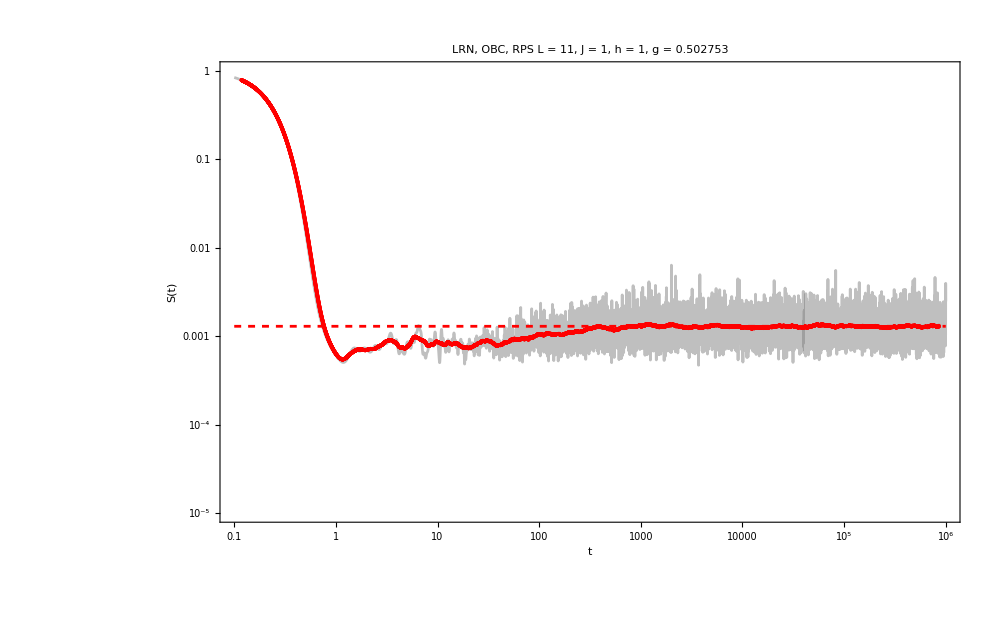

```mathematica
Show[{ListLogLogPlot[{Transpose[{tlist,Mean[time]}],MovingAverage[Transpose[{tlist,Mean[time]}],200]},PlotStyle->{Directive[Gray,Opacity[0.5]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-5,1}},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[hlist[[h]]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],LogLogPlot[Mean[ipr],{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Black,Dashed],Directive[Red,Dashed]}]}]
```

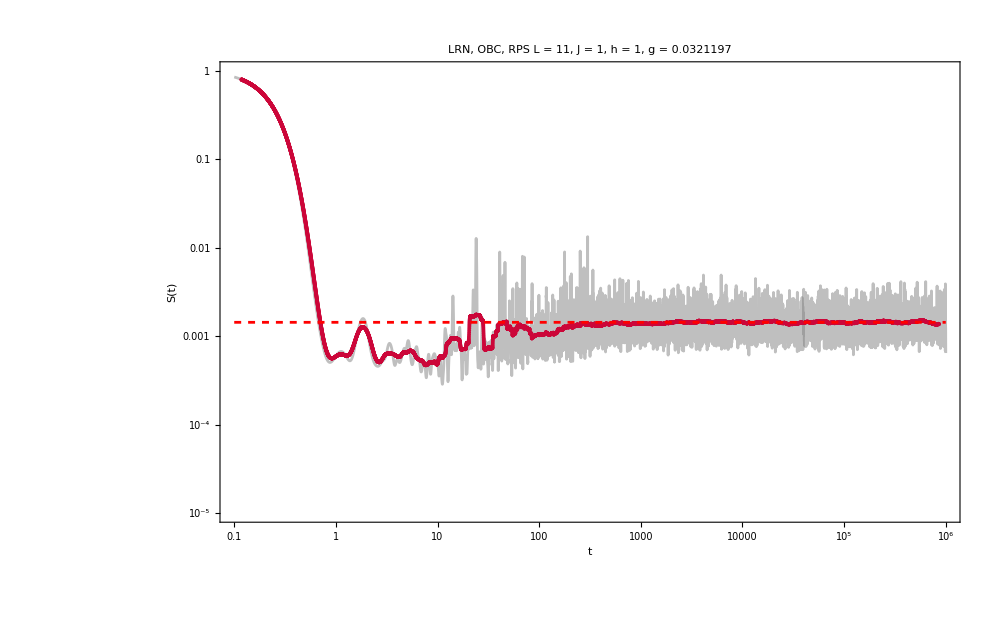

```mathematica
Show[{ListLogLogPlot[{Transpose[{tlist,Mean[time]}],MovingAverage[Transpose[{tlist,Mean[time]}],200]},PlotStyle->{Directive[Gray,Opacity[0.5]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-5,1}},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[hlist[[h]]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],LogLogPlot[Mean[ipr],{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Black,Dashed],Directive[Red,Dashed]}]}]
```

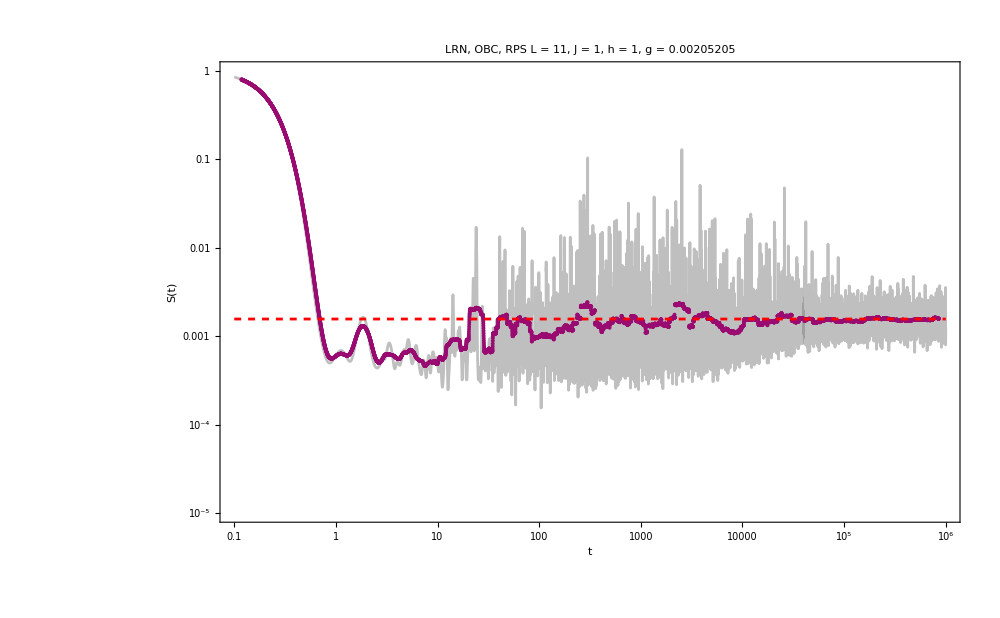

```mathematica
Show[{ListLogLogPlot[{Transpose[{tlist,Mean[time]}],MovingAverage[Transpose[{tlist,Mean[time]}],200]},PlotStyle->{Directive[Gray,Opacity[0.5]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-5,1}},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[hlist[[h]]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],LogLogPlot[Mean[ipr],{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Black,Dashed],Directive[Red,Dashed]}]}]
```

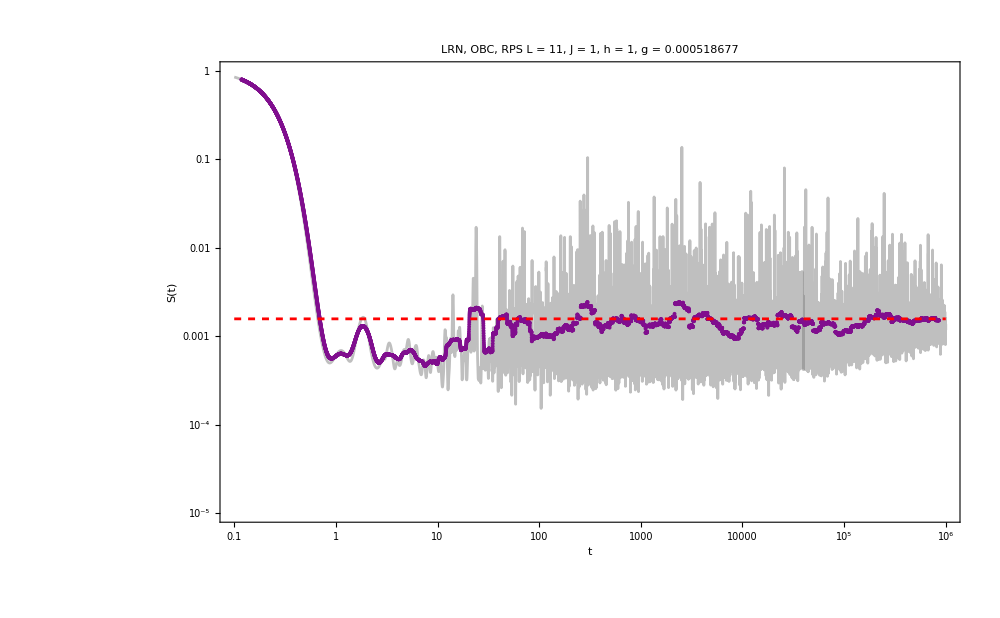

```mathematica
Show[{ListLogLogPlot[{Transpose[{tlist,Mean[time]}],MovingAverage[Transpose[{tlist,Mean[time]}],200]},PlotStyle->{Directive[Gray,Opacity[0.5]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-5,1}},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[hlist[[h]]],35,Black],FrameLabel->{Style["t",25,Black],Style["S(t)",25,Black]}],LogLogPlot[Mean[ipr],{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Black,Dashed],Directive[Red,Dashed]}]}]
```

# Svn

```mathematica
J=1;
g=1;
tlist=Table[10^i,{i,-1,6,0.00070}];
tlist//Length
```

10001

```mathematica
hlist=Table[(7Sqrt[5])^i,{i,-4,0,0.25}];
hlist=Sort[AppendTo[hlist,0.0]];
hlist=hlist[[1;;-1;;2]]
hlist//Length
n=Length[hlist]+1;
reds=Table[Blend[{RGBColor[0.1,0.1,1],RGBColor[1,0,0]},t],{t,1/(n-1),1,1/(n-1)}];
cf=Blend[{{0,Blue},{0.5,Purple},{1,Red}},#]&;
```

{0.,0.000033137,0.000131101,0.000518677,0.00205205,0.00811857,0.0321197,0.127076,0.502753}

9

```mathematica
L=10;
```

```mathematica
visited=ConstantArray[False,2^L,SparseArray];
evenMap={};
oddMap={};
Do[
If[!visited[[i+1]],
j=revIndex[i,L];
visited[[i+1]]=True;
visited[[j+1]]=True;
If[i==j,AppendTo[evenMap,{i}],AppendTo[evenMap,{i,j}];
AppendTo[oddMap,{i,j}];
];]
,{i,0,(2^L)-1}];
```

```mathematica
allvalues={};
allvectors={};

Do[

Ha=IsingHamiltonian[1,hlist[[h]],J,L,BoundaryConditions->"Open"];
system=BlockDiagonalize[Ha, Symmetry->"Parity"];
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[1]]]]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Quiet[Eigensystem[system[[2]]]]]]];
neweven=Table[ExpandBlockVector[i,evenMap,"even",L],{i,eveneigenvec}];
newodd=Table[ExpandBlockVector[i,oddMap,"odd",L],{i,oddeigenvec}];
allvecs=Join[neweven,newodd];
allvals=Join[eveneigenval,oddeigenval];
newall=SortBy[Transpose[{allvals,allvecs}],First];
allvecs=newall[[All,2]];
allvals=newall[[All,1]];

AppendTo[allvalues,allvals];
AppendTo[allvectors,allvecs];

,{h,Length[hlist]}];
```

```mathematica
productstatesfull=Table[RandomChainProductState[L],{i,10}];
```

```mathematica
h=-1;
```

```mathematica
entropy=ParallelTable[new[L,allvalues[[h]],allvectors[[h]],productstatesfull[[1]],t],{t,tlist}];
```

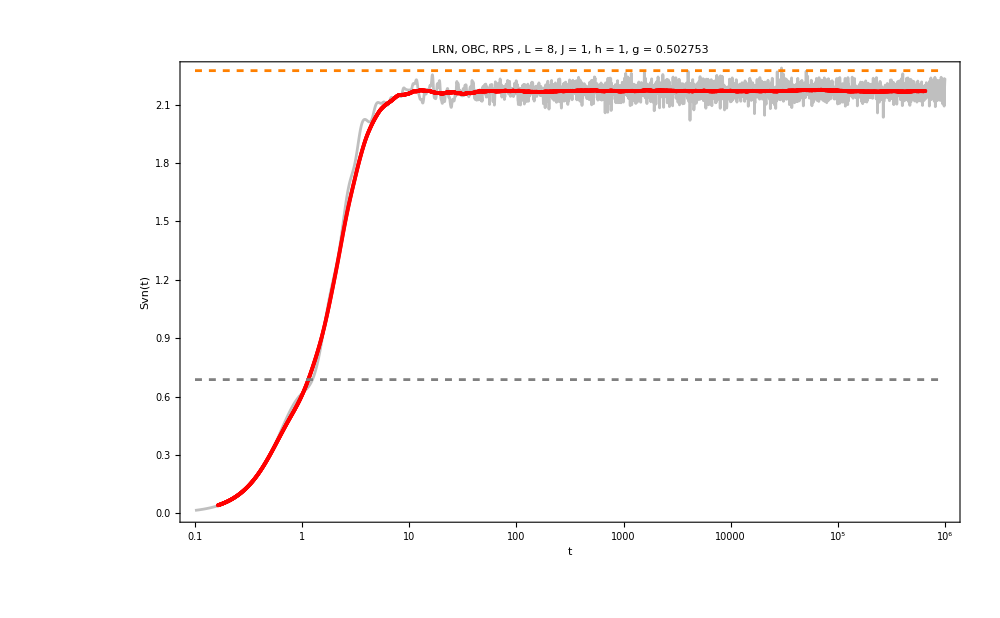

```mathematica
ploten=Show[{ListLogLinearPlot[{Transpose[{tlist,entropy}],MovingAverage[Transpose[{tlist,entropy}],200]},PlotStyle->{Directive[Gray,Opacity[0.50]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[hlist[[h]]],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}],LogLinearPlot[{pageEntropy[1,7],pageEntropy[4,4]},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{Directive[Gray,Dashed],Directive[Orange,Dashed],Directive[Brown,Dashed],Directive[Purple,Dashed],Directive[Blue,Dashed],Directive[Blue,Dashed]}]},PlotRange->{All,{0,pageEntropy[4,4]}}]
```

```mathematica
Clear[psit];
psit=Compile[{{eigenval,_Real,1},{ck,_Complex,1},{tlist,_Real,1}},
Module[{Dloc,Tloc,out,i,j},
Dloc=Length[eigenval];
Tloc=Length[tlist];
out=Table[0.+0. I,{Dloc},{Tloc}];
(*preallocate complex matrix*)
For[j=1,j<=Tloc,j++,
For[i=1,i<=Dloc,i++,
out[[i,j]]=Exp[-I*eigenval[[i]]*tlist[[j]]]*ck[[i]];];];
out],
CompilationTarget->"WVM"];
Clear[new];
new[colVec_]:=Module[{M,s,p},
M=ArrayReshape[colVec,{2^(L/2),2^(L/2)}];
Total[Map[VNentropy,(Chop[SingularValueList[M]])^2]]/Log[2^(L/2)]];
```

```mathematica
hlist
```

{0.,0.000033137,0.000131101,0.000518677,0.00205205,0.00811857,0.0321197,0.127076,0.502753}

```mathematica
plots={};
Do[

entropy={};
Do[
ck=Conjugate[allvectors[[h]]].j;
Developer`ToPackedArray/@{allvalues[[h]],allvectors[[h]],ck,tlist};
t=psit[allvalues[[h]],ck,tlist];
Developer`ToPackedArray[t]; 
final=Transpose[allvectors[[h]]].t;
Developer`ToPackedArray[final];
test=ParallelMap[new,Transpose[final]];
AppendTo[entropy,test];
,{j,productstatesfull}];

ploten=Show[{ListLogLinearPlot[{Transpose[{tlist,Mean[entropy]}],MovingAverage[Transpose[{tlist,Mean[entropy]}],200]},PlotStyle->{Directive[Gray,Opacity[0.50]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->1000,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["LRN, OBC, RPS , L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1, g = "<>ToString[hlist[[h]]],35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]},PlotRange->{All,{0,1}}];
AppendTo[plots,ploten];

,{h,Length[hlist]}];
```

```mathematica
ListAnimate[plots,AnimationRunning->False]
```

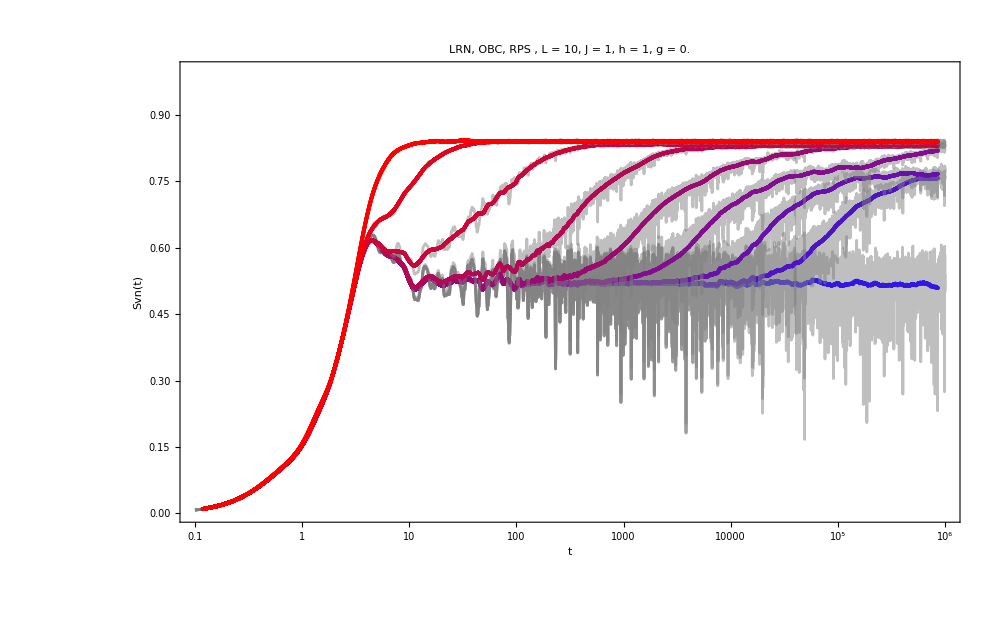

```mathematica
Show[plots]
```